This is a continuation of ToGraph.nb

## Graphs for all systems in the same scale

### Plotting data

```mathematica
(***NOTA: Los modelos 7 y 9 deben ser igual al 1 *****************)
modelo1="controlGA, One UnR G ";
modelo2="controlGA, One R G ";
modelo3="controlGA, AI_A_A ";
modelo4="controlGA, AI_A_I ";
modelo5="controlGA, AI_I_A ";
modelo6="controlGA, AI_I_I ";
modelo7="controlGA, A→I A_A";
modelo8="controlGA, A→I A_I";
modelo7b="controlGA, A→I I_A";
modelo8b="controlGA, A→I I_I";
modelo9="controlGA, I-A A_A";
modelo10="controlGA, I-A A_I";
modelo9b="controlGA, I-A I_A";modelo10b="controlGA, I-A I_I";
```

#### FF for mRNA and protein

```mathematica
(**********************mRNA)
```

```mathematica
ffmRNA4[[1,1]]=ffmRNA5[[1,1]]=ffmRNA8[[1,1]]=ffmRNA10[[1,1]]=ffmRNA7b[[1,1]]=ffmRNA9b[[1,1]]=3;
ffmRNA4[[1,2]]=ffmRNA5[[1,2]]=ffmRNA8[[1,2]]=ffmRNA10[[1,2]]=ffmRNA7b[[1,2]]=ffmRNA9b[[1,2]]=0.45;(* OJO!!! ESTO SE HACE PARA PORDER REESCALAR Y PONER TODAS LAS GRAFICAS EN LA MISMA ESCALA. SE HACE PARA AQUELLOS DATOS QUE NO CONTIENEN EL MÁXIMO VALOR DEL PLOTRANGE, AL PODER INCLUIR ESTE VALOR DENTRO DE LOS DATOS SE PUEDE RE-ESCALAR*)
```

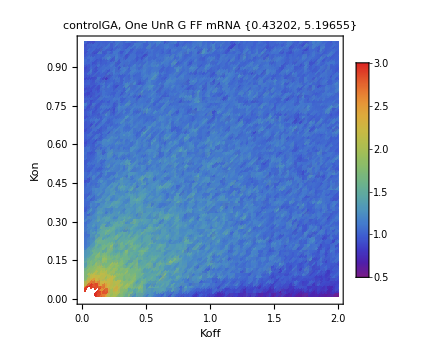
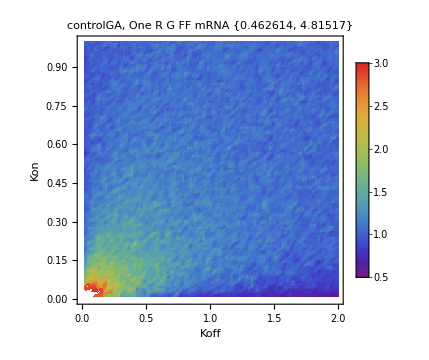
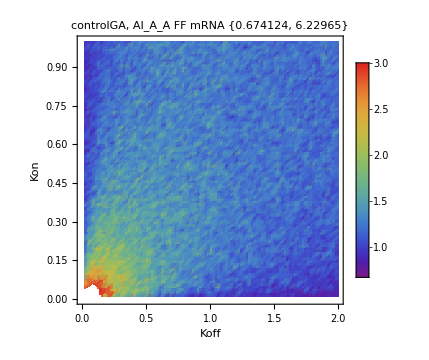
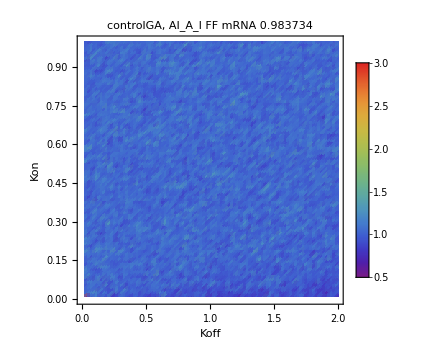
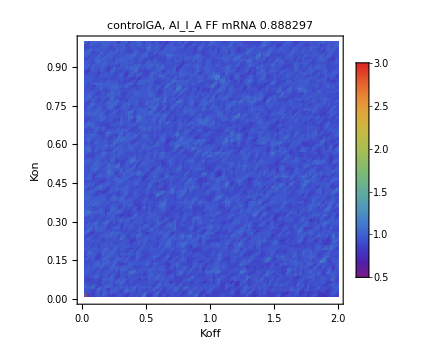
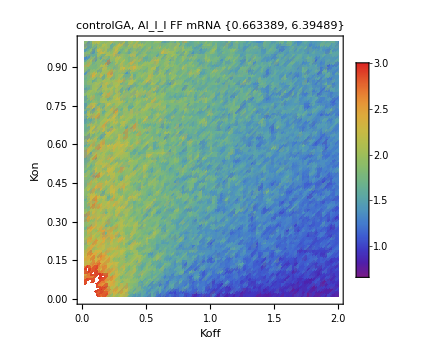
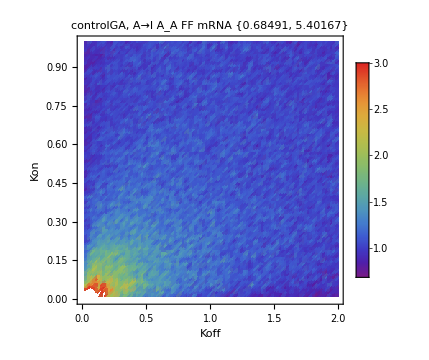
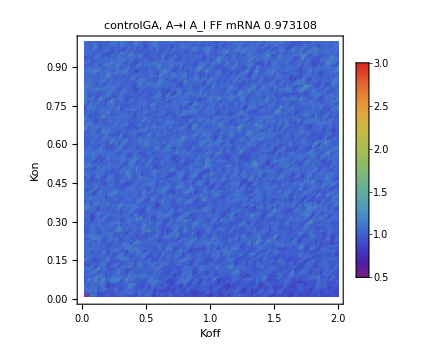

```mathematica
Table[ListDensityPlot[i[[1]],PlotLabel->i[[2]],PlotLegends->Automatic,LabelStyle->Directive[Black,20],Frame-> True,FrameLabel->{"Koff","Kon"}(*{"Koff","Kon"}{"KdmRNA","Koff"}{"Kdp","KdmRNA"}*),DataRange->{{0.02,2},{0.01,1}(*{0.001,0.1},{0.01,1}{0.02,2}*)},FrameTicksStyle->Directive[Black,21],PlotRange-> {0.45,3},ColorFunction->"Rainbow",ImageSize->Medium],{i,{{ffmRNA1,ToString[modelo1]<>" \n FF mRNA "<>ToString[MinMax@Flatten@ffmRNA1]},{ffmRNA2,ToString[modelo2]<>" \n FF mRNA "<>ToString[MinMax@Flatten@ffmRNA2]},{ffmRNA3,ToString[modelo3]<>" \n FF mRNA "<>ToString[MinMax@Flatten@ffmRNA3]},{ffmRNA4,ToString[modelo4]<>" \n FF mRNA "<>ToString[Mean@Flatten@ffmRNA4]},{ffmRNA5,ToString[modelo5]<>" \n FF mRNA "<>ToString[Mean@Flatten@ffmRNA5]},{ffmRNA6,ToString[modelo6]<>" \n FF mRNA "<>ToString[MinMax@Flatten@ffmRNA6]},{ffmRNA7,ToString[modelo7]<>" \n FF mRNA "<>ToString[MinMax@Flatten@ffmRNA7]},{ffmRNA8,ToString[modelo8]<>" \n FF mRNA "<>ToString[Mean@Flatten@ffmRNA8]},
{ffmRNA7b,ToString[modelo7b]<>" \n FF mRNA "<>ToString[MinMax@Flatten@ffmRNA7b]},{ffmRNA8b,ToString[modelo8b]<>" \n FF mRNA "<>ToString[Mean@Flatten@ffmRNA8b]},{ffmRNA9,ToString[modelo9]<>" \n FF mRNA "<>ToString[MinMax@Flatten@ffmRNA9]},{ffmRNA10,ToString[modelo10]<>" \n FF mRNA "<>ToString[Mean@Flatten@ffmRNA10]},
{ffmRNA9b,ToString[modelo9b]<>" \n FF mRNA "<>ToString[MinMax@Flatten@ffmRNA9b]},{ffmRNA10b,ToString[modelo10b]<>" \n FF mRNA "<>ToString[Mean@Flatten@ffmRNA10b]}}}]
```

```mathematica
(******************************protein)
```

```mathematica
ffProtein4[[1,1]]=ffProtein5[[1,1]]=ffProtein8[[1,1]]=ffProtein10[[1,1]]=ffProtein7b[[1,1]]=ffProtein9b[[1,1]]=100;
ffProtein4[[1,2]]=ffProtein5[[1,2]]=ffProtein8[[1,2]]=ffProtein10[[1,2]]=ffProtein7b[[1,2]]=ffProtein9b[[1,2]]=15;(* OJO!!! ESTO SE HACE PARA PORDER REESCALAR Y PONER TODAS LAS GRAFICAS EN LA MISMA ESCALA. SE HACE PARA AQUELLOS DATOS QUE NO CONTIENEN EL MÁXIMO VALOR DEL PLOTRANGE, AL PODER INCLUIR ESTE VALOR DENTRO DE LOS DATOS SE PUEDE RE-ESCALAR*)
```

```mathematica
Table[ListDensityPlot[i[[1]],PlotLabel->i[[2]],PlotLegends->Automatic,FrameTicksStyle->Directive[Black,21],LabelStyle->Directive[Black,20],Frame-> True,FrameLabel->{"Koff","Kon"}(*{"Koff","Kon"}{"KdmRNA","Koff"}{"Kdp","KdmRNA"}*),DataRange->{{0.02,2},{0.01,1}(*{0.001,0.1},{0.01,1}{0.02,2}*)},PlotRange-> {15,100},ColorFunction->"Rainbow",ImageSize->Medium],{i,{{ffProtein1,ToString[modelo1]<>" \n FF protein "<>ToString[MinMax@Flatten@ffProtein1]},{ffProtein2,ToString[modelo2]<>" \n FF protein "<>ToString[MinMax@Flatten@ffProtein2]},{ffProtein3,ToString[modelo3]<>" \n FF protein "<>ToString[MinMax@Flatten@ffProtein3]},{ffProtein4,ToString[modelo4]<>" \n FF protein "<>ToString[Mean@Flatten@ffProtein4]},
{ffProtein5,ToString[modelo5]<>" \n FF protein "<>ToString[Mean@Flatten@ffProtein5]},{ffProtein6,ToString[modelo6]<>" \n FF protein "<>ToString[MinMax@Flatten@ffProtein6]},{ffProtein7,ToString[modelo7]<>" \n FF protein "<>ToString[MinMax@Flatten@ffProtein7]},{ffProtein8,ToString[modelo8]<>" \n FF protein "<>ToString[Mean@Flatten@ffProtein8]},
{ffProtein7b,ToString[modelo7b]<>" \n FF protein "<>ToString[MinMax@Flatten@ffProtein7b]},{ffProtein8b,ToString[modelo8b]<>" \n FF protein "<>ToString[Mean@Flatten@ffProtein8b]},
{ffProtein9,ToString[modelo9]<>" \n FF protein "<>ToString[MinMax@Flatten@ffProtein9]},{ffProtein10,ToString[modelo10]<>" \n FF protein "<>ToString[Mean@Flatten@ffProtein10]},
{ffProtein9b,ToString[modelo9b]<>" \n FF protein "<>ToString[MinMax@Flatten@ffProtein9b]},{ffProtein10b,ToString[modelo10b]<>" \n FF protein "<>ToString[Mean@Flatten@ffProtein10b]}}}]
```

#### CV2 for mRNA and protein

```mathematica
(*************************************************mRNA)
```

```mathematica
cv2mRNA4[[1,1]]=cv2mRNA5[[1,1]]=cv2mRNA8[[1,1]]=cv2mRNA10[[1,1]]=cv2mRNA7b[[1,1]]=cv2mRNA9b[[1,1]]=3;
cv2mRNA4[[1,2]]=cv2mRNA5[[1,2]]=cv2mRNA8[[1,2]]=cv2mRNA10[[1,2]]=cv2mRNA7b[[1,2]]=cv2mRNA9b[[1,2]]=0.45;(* OJO!!! ESTO SE HACE PARA PORDER REESCALAR Y PONER TODAS LAS GRAFICAS EN LA MISMA ESCALA. SE HACE PARA AQUELLOS DATOS QUE NO CONTIENEN EL MÁXIMO VALOR DEL PLOTRANGE, AL PODER INCLUIR ESTE VALOR DENTRO DE LOS DATOS SE PUEDE RE-ESCALAR*)
```

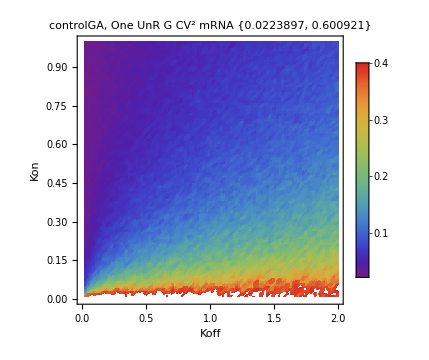
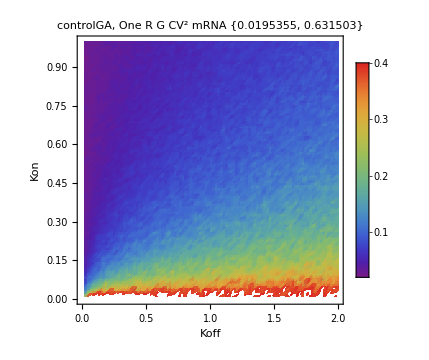
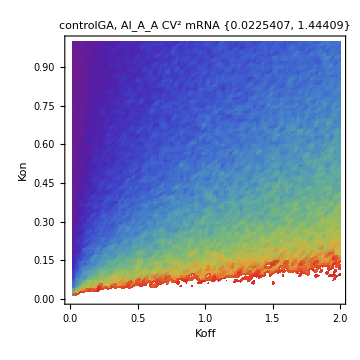
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[ListDensityPlot[i[[1]],PlotLabel->i[[2]],FrameTicksStyle->Directive[Black,21],LabelStyle->Directive[Black,20],PlotLegends->Automatic,Frame-> True,FrameLabel->{"Koff","Kon"}(*{"Koff","Kon"}{"KdmRNA","Koff"}{"Kdp","KdmRNA"}*),DataRange->{{0.02,2},{0.01,1}(*{0.001,0.1},{0.01,1}{0.02,2}*)},PlotRange->{0.02,0.4},ColorFunction->"Rainbow",ImageSize->Medium],{i,{{cv2mRNA1,ToString[modelo1]<>" \n CV^2 mRNA "<>ToString[MinMax@Flatten@cv2mRNA1]},{cv2mRNA2,ToString[modelo2]<>" \n CV^2  mRNA "<>ToString[MinMax@Flatten@cv2mRNA2]},{cv2mRNA3,ToString[modelo3]<>" \n CV^2  mRNA "<>ToString[MinMax@Flatten@cv2mRNA3]},{cv2mRNA4,ToString[modelo4]<>" \n CV^2  mRNA "<>ToString[Mean@Flatten@cv2mRNA4]},{cv2mRNA5,ToString[modelo5]<>" \n CV^2  mRNA "<>ToString[Mean@Flatten@cv2mRNA5]},{cv2mRNA6,ToString[modelo6]<>" \n CV^2  mRNA "<>ToString[MinMax@Flatten@cv2mRNA6]},{cv2mRNA7,ToString[modelo7]<>" \n CV^2  mRNA "<>ToString[MinMax@Flatten@cv2mRNA7]},{cv2mRNA8,ToString[modelo8]<>" \n CV^2  mRNA "<>ToString[Mean@Flatten@cv2mRNA8]},{cv2mRNA7b,ToString[modelo7b]<>" \n CV^2  mRNA "<>ToString[MinMax@Flatten@cv2mRNA7b]},{cv2mRNA8b,ToString[modelo8b]<>" \n CV^2  mRNA "<>ToString[Mean@Flatten@cv2mRNA8b]},{cv2mRNA9,ToString[modelo9]<>" \n CV^2  mRNA "<>ToString[MinMax@Flatten@cv2mRNA9]},{cv2mRNA10,ToString[modelo10]<>" \n CV^2  mRNA "<>ToString[Mean@Flatten@cv2mRNA10]},{cv2mRNA9b,ToString[modelo9b]<>" \n CV^2  mRNA "<>ToString[MinMax@Flatten@cv2mRNA9b]},{cv2mRNA10b,ToString[modelo10b]<>" \n CV^2  mRNA "<>ToString[Mean@Flatten@cv2mRNA10b]}}}]
```

```mathematica
(*************************************************mRNA)
```

```mathematica
Table[ListDensityPlot[i[[1]],PlotLabel->i[[2]],FrameTicksStyle->Directive[Black,21],LabelStyle->Directive[Black,20],PlotLegends->Automatic,Frame-> True,FrameLabel->{"Koff","Kon"}(*{"Koff","Kon"}{"KdmRNA","Koff"}{"Kdp","KdmRNA"}*),DataRange->{{0.02,2},{0.01,1}(*{0.001,0.1},{0.01,1}{0.02,2}*)},PlotRange->{0.6,4},ColorFunction->"Rainbow",ImageSize->Medium],{i,{{cv2mRNA1,ToString[modelo1]<>" \n CV^2 mRNA "<>ToString[MinMax@Flatten@cv2mRNA1]},{cv2mRNA2,ToString[modelo2]<>" \n CV^2  mRNA "<>ToString[MinMax@Flatten@cv2mRNA2]},{cv2mRNA3,ToString[modelo3]<>" \n CV^2  mRNA "<>ToString[MinMax@Flatten@cv2mRNA3]},{cv2mRNA4,ToString[modelo4]<>" \n CV^2  mRNA "<>ToString[Mean@Flatten@cv2mRNA4]},{cv2mRNA5,ToString[modelo5]<>" \n CV^2  mRNA "<>ToString[Mean@Flatten@cv2mRNA5]},{cv2mRNA6,ToString[modelo6]<>" \n CV^2  mRNA "<>ToString[MinMax@Flatten@cv2mRNA6]},{cv2mRNA7,ToString[modelo7]<>" \n CV^2  mRNA "<>ToString[MinMax@Flatten@cv2mRNA7]},{cv2mRNA8,ToString[modelo8]<>" \n CV^2  mRNA "<>ToString[Mean@Flatten@cv2mRNA8]},{cv2mRNA7b,ToString[modelo7b]<>" \n CV^2  mRNA "<>ToString[MinMax@Flatten@cv2mRNA7b]},{cv2mRNA8b,ToString[modelo8b]<>" \n CV^2  mRNA "<>ToString[Mean@Flatten@cv2mRNA8b]},{cv2mRNA9,ToString[modelo9]<>" \n CV^2  mRNA "<>ToString[MinMax@Flatten@cv2mRNA9]},{cv2mRNA10,ToString[modelo10]<>" \n CV^2  mRNA "<>ToString[Mean@Flatten@cv2mRNA10]},{cv2mRNA9b,ToString[modelo9b]<>" \n CV^2  mRNA "<>ToString[MinMax@Flatten@cv2mRNA9b]},{cv2mRNA10b,ToString[modelo10b]<>" \n CV^2  mRNA "<>ToString[Mean@Flatten@cv2mRNA10b]}}}]
```

```mathematica
(*************************************************protein)
```

```mathematica
cv2Protein4[[1,1]]=cv2Protein5[[1,1]]=cv2Protein8[[1,1]]=cv2Protein10[[1,1]]=cv2Protein7b[[1,1]]=cv2Protein9b[[1,1]]=1.65;
cv2Protein4[[1,2]]=cv2Protein5[[1,2]]=cv2Protein8[[1,2]]=cv2Protein10[[1,2]]=cv2Protein7b[[1,2]]=cv2Protein9b[[1,2]]=0.3;(* OJO!!! ESTO SE HACE PARA PORDER REESCALAR Y PONER TODAS LAS GRAFICAS EN LA MISMA ESCALA. SE HACE PARA AQUELLOS DATOS QUE NO CONTIENEN EL MÁXIMO VALOR DEL PLOTRANGE, AL PODER INCLUIR ESTE VALOR DENTRO DE LOS DATOS SE PUEDE RE-ESCALAR*)
```

```mathematica
Table[ListDensityPlot[i[[1]],PlotLabel->i[[2]],FrameTicksStyle->Directive[Black,21],LabelStyle->Directive[Black,20],PlotLegends->Automatic,Frame-> True,FrameLabel->{"Koff","Kon"}(*{"Koff","Kon"}{"KdmRNA","Koff"}{"Kdp","KdmRNA"}*),DataRange->{{0.02,2},{0.01,1}(*{0.001,0.1},{0.01,1}{0.02,2}*)},PlotRange->{0.01,0.25},ColorFunction->"Rainbow",ImageSize->Medium],{i,{{cv2Protein1,ToString[modelo1]<>" \n CV^2  protein "<>ToString[MinMax@Flatten@cv2Protein1]},{cv2Protein2,ToString[modelo2]<>" \n CV^2  protein "<>ToString[MinMax@Flatten@cv2Protein2]},{cv2Protein3,ToString[modelo3]<>" \n CV^2  protein "<>ToString[MinMax@Flatten@cv2Protein3]},
{cv2Protein4,ToString[modelo4]<>" \n CV^2  protein "<>ToString[Mean@Flatten@cv2Protein4]},
{cv2Protein5,ToString[modelo5]<>" \n CV^2  protein "<>ToString[Mean@Flatten@cv2Protein5]},{cv2Protein6,ToString[modelo6]<>" \n CV^2  protein "<>ToString[MinMax@Flatten@cv2Protein6]},{cv2Protein7,ToString[modelo7]<>" \n CV^2  protein "<>ToString[MinMax@Flatten@cv2Protein7]},
{cv2Protein8,ToString[modelo8]<>" \n CV^2  protein "<>ToString[Mean@Flatten@cv2Protein8]},
{cv2Protein7b,ToString[modelo7b]<>" \n CV^2  protein "<>ToString[MinMax@Flatten@cv2Protein7b]},
{cv2Protein8b,ToString[modelo8b]<>" \n CV^2  protein "<>ToString[Mean@Flatten@cv2Protein8b]},
{cv2Protein9,ToString[modelo9]<>" \n CV^2  protein "<>ToString[MinMax@Flatten@cv2Protein9]},{cv2Protein10,ToString[modelo10]<>" \n CV^2  protein "<>ToString[Mean@Flatten@cv2Protein10]},
{cv2Protein9b,ToString[modelo9b]<>" \n CV^2  protein "<>ToString[MinMax@Flatten@cv2Protein9b]},{cv2Protein10b,ToString[modelo10b]<>" \n CV^2  protein "<>ToString[Mean@Flatten@cv2Protein10b]}}}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(*************************************************protein)
```

```mathematica
Table[ListDensityPlot[i[[1]],PlotLabel->i[[2]],FrameTicksStyle->Directive[Black,21],LabelStyle->Directive[Black,20],PlotLegends->Automatic,Frame-> True,FrameLabel->{"Koff","Kon"}(*{"Koff","Kon"}{"KdmRNA","Koff"}{"Kdp","KdmRNA"}*),DataRange->{{0.02,2},{0.01,1}(*{0.001,0.1},{0.01,1}{0.02,2}*)},PlotRange->{0.3,1.65},ColorFunction->"Rainbow",ImageSize->Medium],{i,{{cv2Protein1,ToString[modelo1]<>" \n CV^2  protein "<>ToString[MinMax@Flatten@cv2Protein1]},{cv2Protein2,ToString[modelo2]<>" \n CV^2  protein "<>ToString[MinMax@Flatten@cv2Protein2]},{cv2Protein3,ToString[modelo3]<>" \n CV^2  protein "<>ToString[MinMax@Flatten@cv2Protein3]},
{cv2Protein4,ToString[modelo4]<>" \n CV^2  protein "<>ToString[Mean@Flatten@cv2Protein4]},
{cv2Protein5,ToString[modelo5]<>" \n CV^2  protein "<>ToString[Mean@Flatten@cv2Protein5]},{cv2Protein6,ToString[modelo6]<>" \n CV^2  protein "<>ToString[MinMax@Flatten@cv2Protein6]},{cv2Protein7,ToString[modelo7]<>" \n CV^2  protein "<>ToString[MinMax@Flatten@cv2Protein7]},
{cv2Protein8,ToString[modelo8]<>" \n CV^2  protein "<>ToString[Mean@Flatten@cv2Protein8]},
{cv2Protein7b,ToString[modelo7b]<>" \n CV^2  protein "<>ToString[MinMax@Flatten@cv2Protein7b]},
{cv2Protein8b,ToString[modelo8b]<>" \n CV^2  protein "<>ToString[Mean@Flatten@cv2Protein8b]},
{cv2Protein9,ToString[modelo9]<>" \n CV^2  protein "<>ToString[MinMax@Flatten@cv2Protein9]},{cv2Protein10,ToString[modelo10]<>" \n CV^2  protein "<>ToString[Mean@Flatten@cv2Protein10]},
{cv2Protein9b,ToString[modelo9b]<>" \n CV^2  protein "<>ToString[MinMax@Flatten@cv2Protein9b]},{cv2Protein10b,ToString[modelo10b]<>" \n CV^2  protein "<>ToString[Mean@Flatten@cv2Protein10b]}}}]
```

#### mean for mRNA and protein

```mathematica
(*************************************************mRNA)
```

```mathematica
Table[ListDensityPlot[i[[1]],PlotLabel->i[[2]],PlotLegends->Automatic,FrameTicksStyle->Directive[Black,21],LabelStyle->Directive[Black,20],Frame-> True,FrameLabel->{"Koff","Kon"}(*{"Koff","Kon"}{"KdmRNA","Koff"}{"Kdp","KdmRNA"}*),DataRange->{{0.02,2},{0.01,1}(*{0.001,0.1},{0.01,1}{0.02,2}*)},PlotRange->{1,35},ColorFunction->"Rainbow",ImageSize->Medium],{i,{{meanmRNA1,ToString[modelo1]<>" \n Mean mRNA "<>ToString[MinMax@Flatten@meanmRNA1//N]},
{meanmRNA2,ToString[modelo2]<>" \n Mean mRNA "<>ToString[MinMax@Flatten@meanmRNA2//N]},
{meanmRNA3,ToString[modelo3]<>" \n Mean mRNA "<>ToString[MinMax@Flatten@meanmRNA3//N]},
{meanmRNA4,ToString[modelo4]<>" \n Mean mRNA "<>ToString[Mean@Flatten@meanmRNA4//N]},
{meanmRNA5,ToString[modelo5]<>" \n Mean mRNA "<>ToString[Mean@Flatten@meanmRNA5//N]},
{meanmRNA6,ToString[modelo6]<>" \n Mean mRNA "<>ToString[MinMax@Flatten@meanmRNA6//N]},
{meanmRNA7,ToString[modelo7]<>" \n Mean mRNA "<>ToString[MinMax@Flatten@meanmRNA7//N]},
{meanmRNA8,ToString[modelo8]<>" \n Mean mRNA "<>ToString[Mean@Flatten@meanmRNA8//N]},
{meanmRNA7b,ToString[modelo7b]<>" \n Mean mRNA "<>ToString[MinMax@Flatten@meanmRNA7b//N]},
{meanmRNA8b,ToString[modelo8b]<>" \n Mean mRNA "<>ToString[Mean@Flatten@meanmRNA8b//N]},
{meanmRNA9,ToString[modelo9]<>" \n Mean mRNA "<>ToString[MinMax@Flatten@meanmRNA9//N]},
{meanmRNA10,ToString[modelo10]<>" \n Mean mRNA "<>ToString[Mean@Flatten@meanmRNA10//N]},
{meanmRNA9b,ToString[modelo9b]<>" \n Mean mRNA "<>ToString[MinMax@Flatten@meanmRNA9b//N]},
{meanmRNA10b,ToString[modelo10b]<>" \n Mean mRNA "<>ToString[Mean@Flatten@meanmRNA10b//N]}}}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(*************************************************mRNA)
```

```mathematica
Table[ListDensityPlot[i[[1]],PlotLabel->i[[2]],FrameTicksStyle->Directive[Black,21],LabelStyle->Directive[Black,20],PlotLegends->Automatic,Frame-> True,FrameLabel->{"Koff","Kon"}(*{"Koff","Kon"}{"KdmRNA","Koff"}{"Kdp","KdmRNA"}*),DataRange->{{0.02,2},{0.01,1}(*{0.001,0.1},{0.01,1}{0.02,2}*)},PlotRange->{0.3,1.2},ColorFunction->"Rainbow",ImageSize->Medium],{i,{{meanmRNA1,ToString[modelo1]<>" \n Mean mRNA "<>ToString[MinMax@Flatten@meanmRNA1//N]},
{meanmRNA2,ToString[modelo2]<>" \n Mean mRNA "<>ToString[MinMax@Flatten@meanmRNA2//N]},
{meanmRNA3,ToString[modelo3]<>" \n Mean mRNA "<>ToString[MinMax@Flatten@meanmRNA3//N]},
{meanmRNA4,ToString[modelo4]<>" \n Mean mRNA "<>ToString[Mean@Flatten@meanmRNA4//N]},
{meanmRNA5,ToString[modelo5]<>" \n Mean mRNA "<>ToString[Mean@Flatten@meanmRNA5//N]},
{meanmRNA6,ToString[modelo6]<>" \n Mean mRNA "<>ToString[MinMax@Flatten@meanmRNA6//N]},
{meanmRNA7,ToString[modelo7]<>" \n Mean mRNA "<>ToString[MinMax@Flatten@meanmRNA7//N]},
{meanmRNA8,ToString[modelo8]<>" \n Mean mRNA "<>ToString[Mean@Flatten@meanmRNA8//N]},
{meanmRNA7b,ToString[modelo7b]<>" \n Mean mRNA "<>ToString[MinMax@Flatten@meanmRNA7b//N]},
{meanmRNA8b,ToString[modelo8b]<>" \n Mean mRNA "<>ToString[Mean@Flatten@meanmRNA8b//N]},
{meanmRNA9,ToString[modelo9]<>" \n Mean mRNA "<>ToString[MinMax@Flatten@meanmRNA9//N]},
{meanmRNA10,ToString[modelo10]<>" \n Mean mRNA "<>ToString[Mean@Flatten@meanmRNA10//N]},
{meanmRNA9b,ToString[modelo9b]<>" \n Mean mRNA "<>ToString[MinMax@Flatten@meanmRNA9b//N]},
{meanmRNA10b,ToString[modelo10b]<>" \n Mean mRNA "<>ToString[Mean@Flatten@meanmRNA10b//N]}}}]
```

```mathematica
(*************************************************protein)
```

```mathematica
Table[ListDensityPlot[i[[1]],PlotLabel->i[[2]],FrameTicksStyle->Directive[Black,21],LabelStyle->Directive[Black,20],PlotLegends->Automatic,Frame-> True,FrameLabel->{"Koff","Kon"}(*{"Koff","Kon"}{"KdmRNA","Koff"}{"Kdp","KdmRNA"}*),DataRange->{{0.02,2},{0.01,1}(*{0.001,0.1},{0.01,1}{0.02,2}*)},PlotRange->{50,2300},ColorFunction->"Rainbow",ImageSize->Medium],{i,{{meanProtein1,ToString[modelo1]<>" \n Mean protein "<>ToString[MinMax@Flatten@meanProtein1//N]},{meanProtein2,ToString[modelo2]<>" \n Mean protein "<>ToString[MinMax@Flatten@meanProtein2//N]},{meanProtein3,ToString[modelo3]<>" \n Mean protein "<>ToString[MinMax@Flatten@meanProtein3//N]},
{meanProtein4,ToString[modelo4]<>" \n Mean protein "<>ToString[Mean@Flatten@meanProtein4//N]},
{meanProtein5,ToString[modelo5]<>" \n Mean protein "<>ToString[Mean@Flatten@meanProtein5//N]},{meanProtein6,ToString[modelo6]<>" \n Mean protein "<>ToString[MinMax@Flatten@meanProtein6//N]},{meanProtein7,ToString[modelo7]<>" \n Mean protein "<>ToString[MinMax@Flatten@meanProtein7//N]},
{meanProtein8,ToString[modelo8]<>" \n Mean protein "<>ToString[Mean@Flatten@meanProtein8//N]},
{meanProtein7b,ToString[modelo7b]<>" \n Mean protein "<>ToString[MinMax@Flatten@meanProtein7b//N]},
{meanProtein8b,ToString[modelo8b]<>" \n Mean protein "<>ToString[Mean@Flatten@meanProtein8b//N]},
{meanProtein9,ToString[modelo9]<>" \n Mean protein "<>ToString[MinMax@Flatten@meanProtein9//N]},{meanProtein10,ToString[modelo10]<>" \n Mean protein "<>ToString[Mean@Flatten@meanProtein10//N]},
{meanProtein9b,ToString[modelo9b]<>" \n Mean protein "<>ToString[MinMax@Flatten@meanProtein9b//N]},{meanProtein10b,ToString[modelo10b]<>" \n Mean protein "<>ToString[Mean@Flatten@meanProtein10b//N]}}}]
```

```mathematica
(*************************************************protein)
```

```mathematica
Table[ListDensityPlot[i[[1]],PlotLabel->i[[2]],PlotLegends->Automatic,FrameTicksStyle->Directive[Black,21],LabelStyle->Directive[Black,20],Frame-> True,FrameLabel->{"Koff","Kon"}(*{"Koff","Kon"}{"KdmRNA","Koff"}{"Kdp","KdmRNA"}*),DataRange->{{0.02,2},{0.01,1}(*{0.001,0.1},{0.01,1}{0.02,2}*)},PlotRange->{10,76},ColorFunction->"Rainbow",ImageSize->Medium],{i,{{meanProtein1,ToString[modelo1]<>" \n Mean protein "<>ToString[MinMax@Flatten@meanProtein1//N]},{meanProtein2,ToString[modelo2]<>" \n Mean protein "<>ToString[MinMax@Flatten@meanProtein2//N]},{meanProtein3,ToString[modelo3]<>" \n Mean protein "<>ToString[MinMax@Flatten@meanProtein3//N]},
{meanProtein4,ToString[modelo4]<>" \n Mean protein "<>ToString[Mean@Flatten@meanProtein4//N]},
{meanProtein5,ToString[modelo5]<>" \n Mean protein "<>ToString[Mean@Flatten@meanProtein5//N]},{meanProtein6,ToString[modelo6]<>" \n Mean protein "<>ToString[MinMax@Flatten@meanProtein6//N]},{meanProtein7,ToString[modelo7]<>" \n Mean protein "<>ToString[MinMax@Flatten@meanProtein7//N]},
{meanProtein8,ToString[modelo8]<>" \n Mean protein "<>ToString[Mean@Flatten@meanProtein8//N]},
{meanProtein7b,ToString[modelo7b]<>" \n Mean protein "<>ToString[MinMax@Flatten@meanProtein7b//N]},
{meanProtein8b,ToString[modelo8b]<>" \n Mean protein "<>ToString[Mean@Flatten@meanProtein8b//N]},
{meanProtein9,ToString[modelo9]<>" \n Mean protein "<>ToString[MinMax@Flatten@meanProtein9//N]},{meanProtein10,ToString[modelo10]<>" \n Mean protein "<>ToString[Mean@Flatten@meanProtein10//N]},
{meanProtein9b,ToString[modelo9b]<>" \n Mean protein "<>ToString[MinMax@Flatten@meanProtein9b//N]},{meanProtein10b,ToString[modelo10b]<>" \n Mean protein "<>ToString[Mean@Flatten@meanProtein10b//N]}}}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## Graphs for constitutive expressions

```mathematica
ffmRNA0[[1,1]]==0.15;ffmRNA0[[-1,9]]==1.4;
```

```mathematica
ListDensityPlot[ffmRNA0,PlotLabel->"GA constitutive \n FF mRNA",PlotLegends->Automatic,Frame-> True,FrameLabel->{"Kdp","KdmRNA"},PlotRange-> {0.15,1.4},(*{"Koff","Kon"}{"KdmRNA","Koff"}{"Kdp","KdmRNA"}*)DataRange->{{0.001,0.1},{0.001,0.1}(*{0.001,0.1},{0.01,1}{0.02,2}*)},ColorFunction->"Rainbow",ImageSize->Medium]
```

-Graphics-

```mathematica
ListDensityPlot[ffProtein0,PlotLabel->"GA constitutive \n FF mRNA",PlotLegends->Automatic,Frame-> True,FrameLabel->{"Kdp","KdmRNA"},PlotRange-> {1,49},(*{"Koff","Kon"}{"KdmRNA","Koff"}{"Kdp","KdmRNA"}*)DataRange->{{0.001,0.1},{0.001,0.1}(*{0.001,0.1},{0.01,1}{0.02,2}*)},ColorFunction->"Rainbow",ImageSize->Medium]
```

-Graphics-

```mathematica
Select[Round[Flatten[ffProtein0]]//Tally,#[[1]]<10&]
```

{{8,1650},{9,1487},{6,655},{7,1240},{5,348},{4,255},{3,84},{2,11}}